# JunoCam Processing 24 - Lens Geometry Control Points from Cruise Stage Star data takes

## Description

### What it does

Extract control points from multiple cruise stage star field data takes into a format usable by the Hugin panorama software to estimate lens correction parameters.

### How it works

A flattening process is applied to each data take to reduce CCD hot pixel artifacts.

Then data takes are merged via addition, to increase the density of detectable control points and to establish linkages around an entire 360° revolution.

Segments (framelets) are reprojected to full CCD sized frames.

Potential control points locations are identified. Control points from each frame are matched with control points nearest the expected location in the subsequent three frames.

Matching control points are output in a Hugin/PanoTools format for use in lens correction parameter optimization.

### How to use it

Download 360° data takes from PDS https://pds-imaging.jpl.nasa.gov/data/juno/JNOJNC_0001/DATA/EDR/CRUISE/ 

The selection criteria for the data takes identified in imgFiles below was:

3-color

360° revolution

low-loss compression (larger compressed file size)

Gzip compress the downloaded .IMG files.

Update imgFilesDirectory and imgFiles in below ControllingParameters section in to point to directory and file names on your system.

Evaluate the notebook. Go have lunch. Scroll through notebook to verify it completed successfully.

Start Hugin in Advanced mode.
Click Add Images... in the Photos tab and add the fullFrame_ image files.  Hit Cancel when prompted for FOV.
Save the Hugin project as initialProject.pto. Close Hugin.
Append the controlPoints_ file to the Hugin project file and force yaw parameter of images to fixed yaw rate:

cat controlPoints_3.1.txt >>initialProject.pto

<initialProject.pto awk 'BEGIN {yaw = 0.0}/^i/{$16 = sprintf ("y%-6.9g", yaw); yaw += 4.441583521; print $0}/^[^i]/{print $0}' >fixedYawProject.pto

Open fixedYawProject.pto in Hugin.
Select Optimize Geometric: Custom Parameters at the bottom of the Photos tab.
Select Optimizer tab that is now visible.
Right-click Unselect All on each column of active parameters (eg. Yaw, Pitch, Roll)
Select Parameters you want to try to optimize (eg, Hfov(v), b, d, e).  The parameters are described at http://wiki.panotools.org/Lens_correction_model
Click Optimize now! 
Note the statistics on the match, and click Yes to apply the changes.
(Optional) After this you can review the distances between matches in the Control Points tab to remove a few outliers, and re-optimize. Note: to review all the matches requires cycling through all the frames with an offset between frames of one, two, and three. Hint: I removed ones in fullFrame_3.1_70.png and _71.png, and between _15.png and _18.png. I didn’t remove outliers that were single points near the edge, hoping these might be needed for a better alignment of blue.

### Caveats

The input data take image (.IMG) dimensions are hard coded.
It only reads PDS .IMG files, not -raw.png files from the missionJuno web site.
The code includes various hard-coded parameters (eg expected pixel shift between frames).
The idea of extracting control points from the merged imagery is a design flaw carried forward from the original concept which was for Hugin to identify the control points.
There is an assumption that the yaw (Juno rotation) rate is the same across frames and data takes.
The fullFrame_ images are rotated 90° counterclockwise so a JunoCam data take appears as a left-to-right horizontal panorama to Hugin. Therefore, the control points and calculated lens parameters are in rotated coordinates.
Hugin has been around for ages, but since its executables come from sourceforge.net and are unsigned, I run it in a VM to be safe.
Maximum memory used is around 2GB.

### Additional Notes

A command like this can be used to look at the frame-to-frame yaw and average yaw if you are optimizing yaw.

grep ^i optYawProjectCulled.pto | sed 's/.* y\([^ ]*\) .* n"\([^"]*\)".*/\1 \2/' | awk '{print $1-prev,$2;prev=$1}' |  cat -n
  grep ^i optYawProjectCulled.pto | sed 's/.* y\([^ ]*\) .* n"\([^"]*\)".*/\1 \2/' | awk '{print $1-prev,$2;prev=$1}' |  sort -n | cat -n | sed -n '3,$p' | awk '{sum+=$2}END{print sum;print FNR,sum/FNR}'
  <optYawProjectCulled.pto awk 'BEGIN {yaw = 0.0}/^i/{$16 = sprintf ("y%-6.9g", yaw); yaw += 4.44186; print $0}/^[^i]/{print $0}' >meanYawProject.pto

The produced lens parameters  v=44.96 b=-0.01045 d=12.99 e=13.89 yield Average control point distance = .252, Standard deviation = .319, Maximum = 3.13. However, imagery processed with these parameters still has a fair amount of misalignment, especially noticeable in blue near the edges.
After a complete run, the slow flat generation can be skipped, by manually evaluating sections starting at Load Merged Segments.

## Code

## Startup

```mathematica
(*Clear["Global`*"]*)
```

```mathematica
startTime=Now
```

## Controlling Parameters

```mathematica
imgFilesDirectory="/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/"
```

```mathematica
imgFiles={(* "JNCE_2016026_00C00058_V01.IMG.gz", excluded because of artifact in blue *)
"JNCE_2016026_00C00059_V01.IMG.gz","JNCE_2016026_00C00060_V01.IMG.gz","JNCE_2016026_00C00061_V01.IMG.gz","JNCE_2016026_00C00062_V01.IMG.gz","JNCE_2016026_00C00063_V01.IMG.gz","JNCE_2016026_00C00070_V01.IMG.gz","JNCE_2016026_00C00071_V01.IMG.gz","JNCE_2016026_00C00072_V01.IMG.gz","JNCE_2016026_00C00073_V01.IMG.gz","JNCE_2016026_00C00074_V01.IMG.gz","JNCE_2016026_00C00080_V01.IMG.gz","JNCE_2016026_00C00081_V01.IMG.gz","JNCE_2016026_00C00082_V01.IMG.gz","JNCE_2016026_00C00083_V01.IMG.gz","JNCE_2016040_00C00094_V01.IMG.gz","JNCE_2016040_00C00095_V01.IMG.gz","JNCE_2016040_00C00096_V01.IMG.gz","JNCE_2016040_00C00097_V01.IMG.gz","JNCE_2016040_00C00098_V01.IMG.gz","JNCE_2016040_00C00099_V01.IMG.gz","JNCE_2016040_00C00105_V01.IMG.gz","JNCE_2016040_00C00106_V01.IMG.gz","JNCE_2016040_00C00107_V01.IMG.gz"}
```

```mathematica
fileList=Map[FileNameJoin[{imgFilesDirectory,#}]&,imgFiles];
```

```mathematica
(*fileList=fileList[[{1,-1}]]*)  (* testing with just two files *)
```

```mathematica
flatClipLevel=3.1; (* Flattened DN values less than this are clipped to 0 *)
```

```mathematica
flatScaleFactor=3; (* Flats multiplied by this before subtracting from image segment *)
```

```mathematica
mergedSegsFilename = FileNameJoin[{imgFilesDirectory,"mergedSegs_"<>ToString[flatClipLevel]<>".mx.gz"}]
```

```mathematica
huginCPsFilename=FileNameJoin[{imgFilesDirectory,"controlPoints_"<>ToString[flatClipLevel]<>".txt"}]
```

```mathematica
fullFramesFilenamePrefix=FileNameJoin[{imgFilesDirectory,"fullFrame_"<>ToString[flatClipLevel]<>"_"}]
```

## Definitions and Functions

### Filename Transformations

```mathematica
imgToFlattenedSegsFilename={".IMG.gz"-> "_flattenedSegs.mx.gz"}
```

```mathematica
imgToFlatFilename={".IMG.gz"-> "_flat_data.mx.gz"}
```

```mathematica
imgToInspectionImageFilename={".IMG.gz"-> "_inspectionImage.png"}
```

### Misc

```mathematica
(*Clear["Global`*"]*)
```

```mathematica
On[Assert]
```

```mathematica
imageInfo[image_]:=ImageMeasurements[image,{"Channels","ColorSpace","DataRange","DataType","Dimensions","SampleDepth","Transparency","Min","Max","Mean","Median","StandardDeviation"},Association];
```

### Decompanding

```mathematica
(* decompanding=Import["/Users/bswift/Pictures/Jupiter/decompanding.txt","Table"]; *)
```

```mathematica
lut={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,67,71,75,79,83,87,91,95,99,103,107,111,115,119,123,127,131,135,139,143,147,151,155,159,163,167,171,175,179,183,187,191,195,199,203,207,211,215,219,223,227,231,235,239,243,247,255,263,271,279,287,295,303,311,319,327,335,343,351,359,367,375,383,391,399,407,415,423,431,439,447,455,463,471,479,487,495,503,511,519,527,535,543,551,559,567,575,583,591,599,607,615,623,631,639,647,655,663,671,679,687,695,703,711,719,727,735,743,751,759,767,775,783,791,799,807,815,823,831,839,847,855,863,871,879,887,895,903,911,919,927,935,943,951,959,967,975,983,991,999,1007,1023,1039,1055,1071,1087,1103,1119,1135,1151,1167,1183,1199,1215,1231,1247,1263,1279,1295,1311,1327,1343,1359,1375,1391,1407,1439,1471,1503,1535,1567,1599,1631,1663,1695,1727,1759,1791,1823,1855,1887,1919,1951,1983,2015,2047,2079,2111,2143,2175,2207,2239,2271,2303,2335,2367,2399,2431,2463,2495,2527,2559,2591,2623,2655,2687,2719,2751,2783,2815,2847,2879}/2879. // Developer`ToPackedArray ;
```

```mathematica
rawToLin=Compile[{{lut,_Real,1},{x,_Integer,1}},lut[[x+1]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True];
```

```mathematica
decompandImage[img_?ImageQ]:=Image[rawToLin[lut,ImageData[img,"Byte"]],"Real32"];
```

Credit for decompand performance optimization to users “Coolwater” and “Henrik Schumacher” at https://mathematica.stackexchange.com/questions/151654

```mathematica
ListPlot[rawToLin[lut,Array[#&,256,0]]]
```

### File Loading

```mathematica
(* deprecated *)
importRaw[imageFilename_]:=Module[{rawImage},
importedImage=Import[imageFilename];

Print[imageInfo[importedImage]];
Assert[1==ImageMeasurements[importedImage,"Channels"]];
Print["decompand Timing=",First[AbsoluteTiming [ rawImage = decompandImage[importedImage];]]];
Print[imageInfo[rawImage]];
Print[ImageHistogram[importedImage]];
Print[ImageHistogram[rawImage]];
rawImage
]
```

```mathematica
promptFilename[string_]:=SystemDialogInput["FileOpen",{"None",{"Image files" -> {"*.jpg","*.JPG","*.jpeg","*.JPEG","*.tif","*.png","*.IMG","*.bz2","*.gz"}}},WindowTitle->string]
```

#### Junocam Filename Format from SIS at PDS

JNCT_YYYYDDD_OOFNNNNN_VXX.ZZZ
JNC: JunoCam
T: product type (E for EDR, R for RDR, and M for map product) YYYY: year at the start of image acquisition
DDD: day-of-year at the start of image acquisition
OO: orbit number (or 00 for all cruise products)
F: filter combination specifier for the image (see Appendix B) NNNNN: image index within that mission phase
V: version
XX: version number starting with “01”
ZZZ: file extension (can be IMG, LBL)

Examples:
JNCE_2016346_03R00112_V02-raw.png

```mathematica
parseJunocamFilename[pathName_String]:= Module[
{assoc},
StringCases[pathName,"JNCE_"
~~date:RegularExpression["\\d+"]
~~ "_"
~~orbit:RegularExpression["\\d+"]
~~filter_
~~ index:RegularExpression["\\d+"]
~~"_V"
~~ version:RegularExpression["\\d+"]
(*~~"-"
~~type: __
~~ ".png"*)
~~ ".IMG"
:> (*{date,orbit,filter,index,version,type}*)
(assoc=<|"fnDate"->date,"fnOrbit"->orbit,"fnFilter"->filter,"fnIndex"->index,"fnVersion"->version,"fnType"->"raw" (* hack *) ,"fnPathName"->pathName|>)];
Append[assoc,"fnBaseName"-> FileNameTake[pathName]]
]
```

```mathematica
partitionRaw[fileInfo_Association]:= Module[
{
rawImage
,imageColumns
,framletRows
,segments
,filters
},
(* if Raw, need to split in to 1 or 3 lists of framelets *)
rawImage=fileInfo[["dnImage"]];
imageColumns=ImageDimensions[rawImage][[2]];
framletRows=128;  (* need to detect when 64 instead of 128 *)
filters={fileInfo[["fnFilter"]]};
If[{"C"}==filters,filters={"B","G","R"}];
segments=AssociationThread[
filters
,Table[ImagePartition[rawImage,{imageColumns,framletRows}][[i;; All;; Length[filters]]],{i,1,Length[filters]}]
];
<|"filters"-> filters,"segments"-> segments|>
]
```

```mathematica
(*parseJunocamFilename["JNCE_2016346_03R00112_V02-raw.png"] (* test fn parsing*) *)
```

```mathematica
(* <|"fnDate"->"2016346","fnOrbit"->"03","fnFilter"->"R","fnIndex"->"00112","fnVersion"->"02","fnType"->"raw","fnPathName"->"JNCE_2016346_03R00112_V02-raw.png","fnBaseName"->"JNCE_2016346_03R00112_V02-raw.png"|> *)
```

Possibly improve OO-ness using suggestion at https://mathematica.stackexchange.com/questions/8690/code-readability-and-object-oriented-code

```mathematica
loadChannelsFn[junocamFileName_]:= Module[
{rawFileName
,fnParts
,importedImage
,dnImage
,channels
},
(*junocamFileName=promptFilename["Select Junocam file"];*)
fnParts=parseJunocamFilename[junocamFileName];
importedImage=Import[junocamFileName,"RawBitmap",ImageSize->{1648,31488}]; (* hack *)
If[fnParts[["fnType"]]=="raw",
dnImage=decompandImage[importedImage];
fnParts=Append[fnParts,"dnImage"->dnImage];
channels=partitionRaw[fnParts];
];
Join[fnParts,<|"importedImage"->importedImage|>,channels]
]
```

```mathematica
loadChannels:= Module[
{junocamFileName},
junocamFileName=promptFilename["Select Junocam file"];
loadChannelsFn[junocamFileName]
]
```

```mathematica
(* Reorder color filter identifiers from native/instrumet BGR to RGB *)
rgbFilters[channelObj_]:= channelObj[["filters"]] /. {"B","G","R"} -> {"R","G","B"}
```

```mathematica
(* Replace filter identifiers with full names *)
rgbFilterNames[channelObj_]:= rgbFilters[channelObj] /. {"R"-> "Red","G"->"Green","B"->"Blue","M"->"Methane","C"->"BRG Color"}
```

```mathematica
(* list (not Association) of segment lists in RGB order if there are three channels, or list with list of single channel segments *)
rgb[channelObj_]:= Values[channelObj[["segments",rgbFilters[channelObj]]]]
```

```mathematica
(*t=loadChannels; Print[Length [rgb[t]]];ColorCombine[ImageAssemble /@ rgb[t]]  (* test *) *)
```

### Flats

#### Identify Dark Segments

```mathematica
identifyDarkSegmentsSlow[imageObj_]:=Block[
{segs,trimmedMeans,darkMetric,orderedDarkMetrics,fractionOfDarkestSegs,darkSegsCount,darkestSegmentIndicies},
segs=rgb[imageObj];
(* TrimmedMeans - average after discarding lower 99% , so brightness of upper 1% as metric of how bright a segment is. *)
AbsoluteTiming[Parallelize[
trimmedMeans=Map[
Table[TrimmedMean[Flatten[ImageData[#]],{trim,0}],{trim,{.99}}]&
,segs,{-1}];
]]   (* 97.3 no parallelize *);
Print[ListLogPlot[Table[trimmedMeans[[#,All,1,cl]],{cl,1,1}],PlotLegends->{99},PlotLabel-> rgbFilterNames[imageObj][[#]],ImageSize->Large,PlotRange->Full] & /@ Range[Length[trimmedMeans]] // Column
];
darkMetric=trimmedMeans[[All,All,1,1]];
(* Look at fraction of pixels that are non-zero as darkness metric *)
orderedDarkMetrics=Map[Ordering,darkMetric];
fractionOfDarkestSegs=.6  (* fraction of segs used to create flats. Brightest segs not not used for flat generation *);
darkSegsCount=Round[fractionOfDarkestSegs Length[orderedDarkMetrics[[1]]]];
darkestSegmentIndicies=Map[Sort[Take[#,darkSegsCount]]&,orderedDarkMetrics];
darkestSegmentIndicies
]
```

```mathematica
identifyDarkSegmentsLessSlow[imageObj_]:=Block[
{segs,trimmedMeans,darkMetric,orderedDarkMetrics,fractionOfDarkestSegs,darkSegsCount,darkestSegmentIndicies},
segs=rgb[imageObj];
(* TrimmedMeans - here is just total of DNs in segment *)
AbsoluteTiming[Parallelize[
trimmedMeans=Map[
{Total[Flatten[ImageData[#]]]}&
,segs,{-1}];
]]   (* 97.3 no parallelize *);
Print[ListLogPlot[Table[trimmedMeans[[#,All,1,cl]],{cl,1,1}],PlotLegends->{"Totals"},PlotLabel-> rgbFilterNames[imageObj][[#]],ImageSize->Large,PlotRange->All] & /@ Range[Length[trimmedMeans]] // Column
];
darkMetric=trimmedMeans[[All,All,1,1]];
(* Look at fraction of pixels that are non-zero as darkness metric *)
orderedDarkMetrics=Map[Ordering,darkMetric];
fractionOfDarkestSegs=.6  (* fraction of segs used to create flats. Brightest segs not not used for flat generation *);
darkSegsCount=Round[fractionOfDarkestSegs Length[orderedDarkMetrics[[1]]]];
darkestSegmentIndicies=Map[Sort[Take[#,darkSegsCount]]&,orderedDarkMetrics];
darkestSegmentIndicies
]
```

```mathematica
identifyDarkSegments=identifyDarkSegmentsSlow (* identifyDarkSegmentsLessSlow *)
```

#### Create Flat

Flat will be per pixel trimmed mean of segments.  Trimming set to exclude a few of the brightest pixels/segments to exclude stars or other outliers.

```mathematica
createFlat[imageObj_,darkestSegmentIndicies_]:=Block[
{segs,darkSegs,darkSegsData,segCountForMean,flatData,flatTotals,flatImages,flatImagesAdj,flatObj},
segs=rgb[imageObj];
(*Dimensions[segs]*)
(*Dimensions[darkestSegmentIndicies]*)

darkSegs=MapThread[#1[[#2,1]]&,{segs,darkestSegmentIndicies}];
(*Dimensions[darkSegs]*)
darkSegsData=Map[ImageData,darkSegs,{-1}];
(*Dimensions[darkSegsData]*)
segCountForMean=Dimensions[darkSegsData][[2]];  (* should be same as darkSegsCount *)
(*Dimensions[Transpose[darkSegsData,{1,4,2,3}]]*)
AbsoluteTiming[Parallelize[flatData=Map[TrimmedMean[#,{0,2/segCountForMean}]&
,Transpose[darkSegsData,{1,4,2,3}],{-2}]];
];  (* 17.2
62.4 serial 29.0 parallel*)
(*Dimensions[flatData]*)
flatTotals=Map[Total[Flatten[#]]&,flatData];
flatImages=Map[Image[#,"Real32"]&,flatData];
(*imageInfo /@ flatImage*)
(flatImagesAdj=ImageAdjust[#,{0,0,1},{0,8/2879.}]& /@ flatImages)(* // Column*);
flatObj=<|"flatData"->flatData,"flatTotals"->flatTotals,"flatImages"->flatImages,"flatImagesAdj"-> flatImagesAdj|>;
flatObj
]
```

```mathematica
(*If[!AssociationQ[allFlats],allFlats=<||>]*)
```

```mathematica
(*key=imageObj[["fnBaseName"]]*)
```

```mathematica
(*AssociateTo[allFlats,key-><|totals->flatTotals,image->flatImage,adjImage-> flatImageAdj|>]*)
```

Totals from Radiation Trending images
“JNCE_2016346_03C00135_V02-raw.png”→<|totals→{23.8548,22.5877,21.3286}
”JNCE_2017033_04C00119_V01-raw.png”→<|totals→{20.4339,19.0603,18.0262}
“JNCE_2017086_05C00121_V01-raw.png”→<|totals→{21.934,20.3304,18.9347}
“JNCE_2017139_06C00142_V01-raw.png”→<|totals→{21.0001,20.1315,17.801}
“JNCE_2017192_07C00074_V01-raw.png”→<|totals→{21.2407,20.0926,18.3445}
“JNCE_2017245_08C00134_V01-raw.png”→<|totals→{23.3757,21.8327,20.2283}  TDI 3

Cruise
“JNCE_2016026_00C00083_V01.IMG.bz2”→<|totals→{66.6138,66.1302,65.544}  smallest low-compressibility image  75% dark seg selection
“JNCE_2016026_00C00083_V01.IMG.bz2”→<|totals→{65.5505,65.1885,64.859}  60% dark seg selection  (to exclude systematic brightening (zodiacal light?))

“JNCE_2016040_00C00107_V01.IMG.bz2”→<|totals→{86.6506,85.2731,83.7331}

```mathematica
(*allFlats[key][totals]/(128 1648) 2879 *) (* Flat magnitude in decompanded/Linear units *)
```

#### Apply flat to segments

```mathematica
applyFlatToSegments[imageObj_,flatObj_]:=Block[
{segs,scaledFlatImages,flattenedSegs,fic},
segs=rgb[imageObj];

(*Dimensions[segs]*)
(*Dimensions[flatImage]*)
scaledFlatImages=Map[ImageMultiply[#,flatScaleFactor]&,flatObj[["flatImages"]]];
(*Dimensions[scaledFlatImage]*)
flattenedSegs=MapThread[(fic=#1;
Map[ImageSubtract[#,fic]&,#2,{-1}])&, {scaledFlatImages,segs}];  (* Nested Map *)
(*Dimensions[flattenedSegs]*)
(*flattenedImage=ImageAdjust[ImageAssemble[flattenedSegs],{0,0,1},{0,8/2879.}]*)
(*imageInfo[flattenedSegs[[1,1,1]]]*)
flattenedSegs
]
```

#### Export flatData

```mathematica
(*Export[StringReplace[imageObj[["fnPathName"]],{"/JNCE_"->"/Flat_data_",".IMG.bz2"->".wdx"}]
,flatData]*)
```

```mathematica
segsToInspectionImage[flattenedSegs_]:=Block[
{adjSegs,colorSegs,inspectionImage},
adjSegs=Map[ImageAdjust[#,{0,0,1},{flatClipLevel/2879,{1,1,.05}8/2879.}]&,flattenedSegs,{-1}];
(*“JNCE_2016026_00C00083_V01.IMG.bz2”->flat scale 3,crush 3.5*)
colorSegs=Transpose[Map[ColorCombine,Transpose[adjSegs,{3,2,1}],{-2}]];
inspectionImage=MaxFilter[ImageAssemble[colorSegs],3];
inspectionImage
]
```

```mathematica
exportFlatData[imageObj_,flatObj_,flattenedSegs_]:=Block[
{flatData,adjSegs,colorSegs,inspectionImage},
flatData=flatObj[["flatData"]];
(*AbsoluteTiming[DumpSave[StringReplace[imageObj[["fnPathName"]],{"/JNCE_"->"/Flat_data_",".IMG.bz2"->".mx"}]
,flatData];];*)  (* export to .wdx super slow *)
AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],imgToFlatFilename ]
,flatData];];  (* export to .wdx super slow *)(*AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],{"/JNCE_"->"/flattenedSegs_",".IMG.bz2"->".mx.bz2"}]
,flattenedSegs];]  ;*)
AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],imgToFlattenedSegsFilename]
,flattenedSegs];]  ;

(* star inspection image *)
adjSegs=Map[ImageAdjust[#,{0,0,1},{flatClipLevel/2879,{1,1,.05}8/2879.}]&,flattenedSegs,{-1}];
(*“JNCE_2016026_00C00083_V01.IMG.bz2”->flat scale 3,crush 3.5*)
colorSegs=Transpose[Map[ColorCombine,Transpose[adjSegs,{3,2,1}],{-2}]];
inspectionImage=MaxFilter[ImageAssemble[colorSegs],3];
AbsoluteTiming[Export[StringReplace[imageObj[["fnPathName"]],imgToInspectionImageFilename ]
,inspectionImage];]  ;
]
```

Export visible flat

Color image to read actual values off Blue channel.

coloredFlats = MapThread[Image[ColorCombine[{#1, #1, #2}], "Bit16"] &, {flatImageAdj, flatImage}]

MapThread[{#1, #2} &, {coloredFlats, rgbFilters[imageObj]}]

Map[imageInfo, coloredFlats]

(* Export derived flats back to source directory *)

MapThread[
 Export[StringReplace[imageObj[["fnPathName"]], "/JNCE_" -> "/Flat_" <> #2 <> "_"], #1]
  &, {coloredFlats, rgbFilters[imageObj]}]

#### Pipeline - process a “.IMG” fileName producing flat related files

```mathematica
imgToFlat[fileName_]:= Block[
{imageObj,darkestSegmentIndicies,flatObj,flattenedSegs},
imageObj=loadChannelsFn[fileName];
Print["fnBaseName = ",imageObj[["fnBaseName"]]];
darkestSegmentIndicies=identifyDarkSegments[imageObj];
Print["darkestSegmentIndicies = ",darkestSegmentIndicies];
flatObj=createFlat[imageObj,darkestSegmentIndicies];
Print["flatTotals = ",flatObj[["flatTotals"]]];
flattenedSegs=applyFlatToSegments[imageObj,flatObj];
exportFlatData[imageObj,flatObj,flattenedSegs];
]
```

#### Merge Segments from flattenedSegFilename

```mathematica
mergeSegsFromFile1[segs_,flattenedSegsFilename_]:=Block[
{mergedSegs,segsToMerge,mergeLevel},
segsToMerge=Import[flattenedSegsFilename];
mergeLevel=ArrayDepth[segs];
mergedSegs=MapThread[ImageAdd,{segs,segsToMerge},mergeLevel]; (* MapThread fails to Parallelize[] *)
Print[FileNameTake[flattenedSegsFilename]<>" Merged "<>DateString["Time"]<>" MaxMemoryUsed "<>ToString[MaxMemoryUsed[]]];
mergedSegs
]
```

```mathematica
clipFlattenedSeg[img_]:=Block[
{},
ImageClip[img,{flatClipLevel/2879,1},{0,1}]
]
```

```mathematica
mergeSegsFromFile[segs_,flattenedSegsFilename_]:=Block[
{mergedSegs,segsToMerge,mergeLevel},
segsToMerge=Import[flattenedSegsFilename];
mergeLevel=ArrayDepth[segs];
mergedSegs=MapThread[
ImageAdd[#1,clipFlattenedSeg[#2]]&,
{segs,segsToMerge},mergeLevel]; (* MapThread fails to Parallelize[] *)
Print[FileNameTake[flattenedSegsFilename]<>" Merged "<>DateString["Time"]<>" MaxMemoryUsed ",MaxMemoryUsed[]];
mergedSegs
]
```

### Startup

```mathematica
$Context
```

```mathematica
Names[$Context<>"*"]
```

```mathematica
MaxMemoryUsed[]
```

## Flatten PDS Images from list

Read list of PDS format (JNCE_*.IMG) path names to be processed into flattened segments and flat data Mathematica data files and inspection image files.

```mathematica
fileList[[{1,-1}]] (* first and last files *)
```

```mathematica
MemoryInUse[] (*2098055552*)
```

```mathematica
AbsoluteTiming[Map[imgToFlat, fileList]]
```

```mathematica
MemoryInUse[](*3843104344*)
```

## Merge Flats

### Setup

```mathematica
fileList[[{1,-1}]] (* first and last files *)
```

```mathematica
flattenedSegsFiles=Map[StringReplace[#,imgToFlattenedSegsFilename ]&,fileList]
```

```mathematica
Length[flattenedSegsFiles]
```

```mathematica
ms1=Map[clipFlattenedSeg,Import[flattenedSegsFiles[[1]]],{-1}]; (* First segs - for use in Fold *)
```

```mathematica
ByteCount[ms1]Length[flattenedSegsFiles] (* memory needed if all segs files were read first - 4984539648 *)
```

### Merge

```mathematica
AbsoluteTiming[mergedSegs=Fold[mergeSegsFromFile,ms1,flattenedSegsFiles[[2;;-1]]];] (*{318.031347,Null} *)
```

```mathematica
AbsoluteTiming[Export[mergedSegsFilename,mergedSegs]](* {2406.362508,"/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/mergedSegs2.mx.bz2"}
{2.120963,"/Users/bswift/Pictures/Jupiter/Junocam/CruisePhase/mergedSegs4.mx.gz"} *)
```

```mathematica
Print[MaxMemoryUsed[]] (* 2017924808 *)
```

## Review Merged Segments

```mathematica
mergedColorImage=ImageAssemble[Transpose[Map[ColorCombine,Transpose[mergedSegs,{3,2,1}],{-2}]]];
```

```mathematica
imageInfo[mergedColorImage]
```

```mathematica
mergedColorImage
```

```mathematica
colorInspectionImage=segsToInspectionImage[mergedSegs]
```

```mathematica
imageInfo[mergedColorImage]
```

## Create Full-frames and Find Control Points

### Load Merged Segments (if not present)

```mathematica
If[Length[mergedSegs]==0,mergedSegs=Import[mergedSegsFilename];]
```

```mathematica
segs=mergedSegs;
```

```mathematica
Dimensions[segs]  (* {3,82,1} expected *)
```

### Segments to Full-Frames

Convert a RGB group of 3 framelets back to a full CCD sized frame based on readout lines

The actual start lines for each 128-line band framelet relative to line 0 at the “top” of the sensor are 291, 456, 611, and 766 with the nominal optic axis at line 600. And the focal length is 10.997mm.

From post http://www.unmannedspaceflight.com/index.php?showtopic=2548&st=465&p=203948&#entry203948

291M, 456B, 611G, and 766R

1600x1200 sensor with 7.4μ sensor  from
http://www.onsemi.com/PowerSolutions/product.do?id=KAI-2020

1640 × 1214 7.4-micron pixels (1600 × 1200 pho- toactive)  from 

FOV 58 per cal report

Using sensor size of 11.84 x 8.88 (from CCD manual) and 10.997 FOV from post and spice into FOV calculator at https://www.scantips.com/lights/fieldofview.html#top
gives FOV 56.59 wide 43.97 high 67.87 diag

Per hugin 10.997 FL * 2.8899 FL multiplier gives 43.97 FOV

```mathematica
31.78/10.997
```

```mathematica
t=;  (* Image of color filters on CCD from Junocam Calibration Report MSSS-JUNOCAM-DOC-0102 *)
```

```mathematica
rgbToFullFrame[rgbList_]:=ColorCombine[{
(*ImagePad[segs[[1,2,1]],{{0,0},{1214-(291-1)-128,291-1}}] (* Methane *)*)
ImagePad[rgbList[[1]],{{0,0},{1214-(766-1)-128,766-1}}] (* Red *)
,ImagePad[rgbList[[2]],{{0,0},{1214-(611-1)-128,611-1}}] (* Green *)
,ImagePad[rgbList[[3]],{{0,0},{1214-(456-1)-128,456-1}}] (* Blue *)
}]
```

```mathematica
MemoryInUse[] (* 948594528 *)
```

#### Export color full-frame images for use in Hugin

```mathematica
addAlpha[img_]:=Block[
{},
SetAlphaChannel[img, Erosion[Dilation[Binarize[img,1/2^20],DiskMatrix[4]],DiskMatrix[2]]]
]
```

```mathematica
AbsoluteTiming[MapIndexed[
Export[fullFramesFilenamePrefix<>ToString[#2[[1]]]<>".png",
addAlpha[
ImageAdjust[
ImageRotate[
rgbToFullFrame[#1[[All,1]]]
]
,{0,0,1},{0,8/2879}] (* scale up to try to make stars visible in Hugin *)
]]&
,Transpose[segs]];
]
```

```mathematica
MemoryInUse[] (* 949501104 *)
```

#### Create grayscale full-frame images to be used for control point identification

```mathematica
AbsoluteTiming[bwfullFrames=Map[
ImageApply[Max,rgbToFullFrame[#[[All,1]]]]&  (* max across channels converts to grayscale image *)
,
Transpose[segs]];
]
```

```mathematica
Dimensions[bwfullFrames]
```

```mathematica
MemoryInUse[] (* 1606080080 *)
```

```mathematica
Clear[segs,mergedSegs]
```

```mathematica
MemoryInUse[] (* 1606082112 *)
```

### Generate Control Points

```mathematica
AbsoluteTiming[cmr=Map[ComponentMeasurements[ImageReflect[ImageRotate[#]],{"Image","Count","IntensityCentroid","TotalIntensity"}(*,#Count>0&*)
,#Count≤ 9&
,"PropertyAssociation"] &
,bwfullFrames
];
]  (* ComponentMeasurements on Rotated images *)
```

```mathematica
Length[cmr]
```

```mathematica
cpCountPerFrame=Map[Length[#["IntensityCentroid"]]&,cmr]
```

```mathematica
Total[cpCountPerFrame]
```

```mathematica
Ordering[cpCountPerFrame]
```

```mathematica
controlPoints=Map[#["IntensityCentroid"]&,cmr];
```

### Match Control Points between frames

```mathematica
matchCPs[imagesPaired_,aFrame_,bFrame_,framesApart_]:=Block[
{expectedShift={115 framesApart,0},searchRadius=2.3+0.5(framesApart-1),
shifted,matched,uncleanPairs,matchedShiftedCPPairs,matchedUNshiftedCPPairs,distances,deltas},

(* Special Case for wrap around CPs.  Value determine by using FindGeometricTransform between last and first bwfullFrames ([[82]] and [[1]] *)
If[Apply[EuclideanDistance,imagesPaired]>4,
expectedShift={6,0}+{115 (framesApart-1),0};
(*searchRadius=2.8;*)
Print[imagesPaired," Expected Shift = ",expectedShift," searchRadius = ",searchRadius];
];
shifted=Map[#+expectedShift&,bFrame];
matched=Nearest[shifted,aFrame,{1,searchRadius}];
uncleanPairs=MapThread[{#1,#2}&,{aFrame,matched}];
matchedShiftedCPPairs=Map[{#[[1]],#[[2,1]]}&,Select[uncleanPairs,#[[2]]≠{}&]];
matchedUNshiftedCPPairs=Map[{#[[1]],#[[2]]-expectedShift}&,matchedShiftedCPPairs,{1}];
distances=Map[EuclideanDistance[#[[1]],#[[2]]]&,matchedShiftedCPPairs];
deltas=Map[Subtract[#[[1]],#[[2]]]&,matchedShiftedCPPairs];
<|"matchedUNshiftedCPPairs"->matchedUNshiftedCPPairs,
"matchedShiftedCPPairs"->matchedShiftedCPPairs,
"deltas"->deltas,"distances"->distances|>
] (* cmr from rotated images, need to shift in x direction *)
```

```mathematica
Clear[cpObj,distances,deltas,matchedShiftedCPPairs,matchedUNshiftedCPPairs,imagesPaired]
(*framesAhead=4*)
Do[
imagesPaired[framesAhead]=MapThread[{#1,#2}&,{Range[Length[controlPoints]],RotateLeft[Range[Length[controlPoints]],framesAhead]}];
cpObj[framesAhead]=Merge[MapThread[matchCPs[#1,#2,#3,framesAhead]&,{imagesPaired[framesAhead],controlPoints,RotateLeft[controlPoints,framesAhead]}]
,Identity];
distances[framesAhead]=cpObj[framesAhead]["distances"];
deltas[framesAhead]=cpObj[framesAhead]["deltas"];
matchedShiftedCPPairs[framesAhead]=cpObj[framesAhead]["matchedShiftedCPPairs"];
matchedUNshiftedCPPairs[framesAhead]=cpObj[framesAhead]["matchedUNshiftedCPPairs"];
,{framesAhead,1,4}
]
```

```mathematica
cpListToString[{{iid1_Integer,iid2_Integer},{{x1_?NumericQ,y1_?NumericQ},{x2_?NumericQ,y2_?NumericQ}}}]:=Block[
{},
StringJoin[Map[ToString,{"c n",iid1-1, " N",iid2-1," x",x1," y",y1," X",x2," Y",y2," t0"}]] (* don't swap x,y because images are rotated for Hugin horizontal panorama format *)
]
```

```mathematica
toCPLists[{imageIndicies_,cpList_}]:=Block[
{
},
Map[{imageIndicies,#}&,cpList]
(*{Length[imageIndicies],Length[cpList]}*)
]
```

```mathematica
cpStringsForHugin=Map[cpListToString,
Flatten[
Map[toCPLists,
Flatten[
Table[
MapThread[{#1,#2}&,
{imagesPaired[framesAhead],matchedUNshiftedCPPairs[framesAhead]
}]
,{framesAhead,1,3}]
,1]
]
,1]
];
```

```mathematica
Length[cpStringsForHugin]
```

```mathematica
cpStringsForHugin[[{1,-1}]] // Column  (* first and last CPs for Hugin .pto *)
```

```mathematica
Export[huginCPsFilename,cpStringsForHugin];
```

Work complete at this point. Following are experiments and and data review.

### Experiments with Mapping control points with predictive functions

```mathematica
Clear[mapx,mapy]
```

```mathematica
mapx=Flatten[
Table[Map[Join[#[[1]],{framesAhead}]-> #[[2,1]]&,Flatten[matchedUNshiftedCPPairs[framesAhead][[1;;-1-framesAhead]],1]]
,{framesAhead,1,3}]
,1];
```

```mathematica
mapy=Flatten[
Table[Map[Join[#[[1]],{framesAhead}]-> #[[2,2]]&,Flatten[matchedUNshiftedCPPairs[framesAhead][[1;;-1-framesAhead]],1]]
,{framesAhead,1,3}]
,1];
```

```mathematica
xRange=MinMax[mapx[[All,1,1]]]
```

```mathematica
yRange=MinMax[mapx[[All,1,2]]]
```

```mathematica
Dimensions[mapx]
```

```mathematica
px=Predict[mapx,PerformanceGoal->"Quality",Method->"GaussianProcess"(* Method->"NeuralNetwork"*)]
```

```mathematica
py=Predict[mapy,PerformanceGoal->"Quality",Method->"GaussianProcess"(* Method->"NeuralNetwork"*)]
```

```mathematica
propsx=PredictorInformation[px,"Properties"]
```

```mathematica
Table[{prop,PredictorInformation[px,prop]},{prop,propsx}] // Column
```

```mathematica
propsy=PredictorInformation[py,"Properties"];
```

```mathematica
Table[{prop,PredictorInformation[py,prop]},{prop,propsy}] // Column
```

```mathematica
Through[{px,py}[{737.144,786.033,1}]] (* "c n0 N1 x737.144 y786.033 X621.727 Y786.5 t0" *)
```

```mathematica
PredictorMeasurements[px,mapx,"ComparisonPlot"]
```

```mathematica
PredictorMeasurements[py,mapy,"ComparisonPlot"]
```

```mathematica
PredictorMeasurements[px,mapx,"MeanDeviation"]
```

```mathematica
PredictorMeasurements[py,mapy,"MeanDeviation"] (*linear 0.7794839896339248,neural 5.606930620862832,gaussian 0.25049099503498434*)
```

```mathematica
PredictorMeasurements[py,mapy,"ResidualHistogram"]
```

```mathematica
Plot[py[{x,1300,1}],Join[{x},xRange]]
```

```mathematica
Plot[py[{x,800,1}],Join[{x},xRange]]
```

```mathematica
Plot[py[{x,100,1}],Join[{x},xRange]]
```

```mathematica
Plot[py[{737.14,786.03,off}],{off,1,3}]
```

```mathematica
Plot[px[{737.14,786.03,off}],{off,1,3}]
```

```mathematica
Plot3D[py[{x,y,2}],Evaluate[Join[{x},xRange]],Evaluate[Join[{y},yRange]]]
```

```mathematica
PredictorMeasurements[px,mapx,"ResidualHistogram"]
```

### Investigating color-color matching

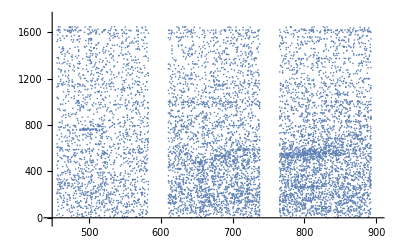

```mathematica
ListPlot[Flatten[controlPoints,1]]
```

```mathematica
ListPlot[Flatten[Table[matchedUNshiftedCPPairs[framesAhead],{framesAhead,1,3}],3]]
```

```mathematica
redRange=766+{-2,+128+2}
```

```mathematica
greenRange=611+{-2,+128+2}
```

```mathematica
blueRange=456+{-2,+128+2}
```

```mathematica
blueBlue=Select[tstCPs,Between[#[[1,1]],blueRange] && Between[#[[2,1]],blueRange]&]
```

```mathematica
redRed=Select[tstCPs,Between[#[[1,1]],redRange] && Between[#[[2,1]],redRange]&]
```

```mathematica
greenGreen=Select[tstCPs,Between[#[[1,1]],greenRange] && Between[#[[2,1]],greenRange]&]
```

```mathematica
imagesPairedXX[1]=MapThread[{#1,#2}&,{ConstantArray[1,Length[controlPoints]],ConstantArray[2,Length[controlPoints]]}]
```

Hack cut/paste/modify of code to produce control points just from the Red-Red, Green-Green, and Blue-Blue overlaps, to investigate lens parameter estimation de-coupled from chromatic aberration.

```mathematica
cpStringsForHuginXX[bb]=Map[cpListToString,
Flatten[
Map[toCPLists,
Flatten[
Table[
MapThread[{#1,#2}&,
{imagesPairedXX[framesAhead],
Map[Select[#,Between[#[[1,1]],blueRange] && Between[#[[2,1]],blueRange]&]&,matchedUNshiftedCPPairs[framesAhead],1]
}]
,{framesAhead,1,1}]
,1]
]
,1]
];
```

```mathematica
cpStringsForHuginXX[gg]=Map[cpListToString,
Flatten[
Map[toCPLists,
Flatten[
Table[
MapThread[{#1,#2}&,
{imagesPairedXX[framesAhead],
Map[Select[#,Between[#[[1,1]],greenRange] && Between[#[[2,1]],greenRange]&]&,matchedUNshiftedCPPairs[framesAhead],1]
}]
,{framesAhead,1,1}]
,1]
]
,1]
];
```

```mathematica
cpStringsForHuginXX[rr]=Map[cpListToString,
Flatten[
Map[toCPLists,
Flatten[
Table[
MapThread[{#1,#2}&,
{imagesPairedXX[framesAhead],
Map[Select[#,Between[#[[1,1]],redRange] && Between[#[[2,1]],redRange]&]&,matchedUNshiftedCPPairs[framesAhead],1]
}]
,{framesAhead,1,1}]
,1]
]
,1]
];
```

```mathematica
cpStringsForHuginXX[bb] //Column
```

```mathematica
cpStringsForHuginXX[gg] //Column
```

```mathematica
cpStringsForHuginXX[rr] //Column
```

### Review CP Matching Results

```mathematica
Table[{i,ListLinePlot[Flatten[matchedShiftedCPPairs[i] ,1],ImageSize->Large]},{i,1,3}] // Column
```

```mathematica
Table[{i,Length[matchedUNshiftedCPPairs[i]]},{i,1,4}]
```

```mathematica
(matchesVframeVshift=Table[{i,Map[Length,distances[i]]},{i,1,4}] )// Column
```

```mathematica
matchesVframe=Apply[Plus,matchesVframeVshift][[2]]
```

```mathematica
Total[matchesVframe] (* different results for different search distances *)(* 2.3 -> 426 *) (* 2.8 -> 460 *) (* 2.3 + 0.5Δ -> 465 *)(* 2.3+0.9Δ -> 484 *)(* 3.3 -> 506 *)
```

```mathematica
Sort[MapIndexed[List,matchesVframe]]
```

```mathematica
Table[{i,Ordering[Map[Length,distances[i]]]},{i,1,4}] // Column
```

```mathematica
Table[{i,ListPlot[Sort[Flatten[distances[i],1]],ImageSize->Small]},{i,1,3}] // Column
```

```mathematica
Table[{i,ListPlot[Flatten[deltas[i],1],ImageSize->Medium]},{i,1,3}] // Column
```

```mathematica
Clear[xVariation,yVariation]
```

```mathematica
Table[{i,ListPlot[xVariation[i]=Sort[Flatten[deltas[i],1][[All,1]]],ImageSize->Small]},{i,1,3}] // Column (* variations in x *)
```

```mathematica
Table[{i,Median[xVariation[i]]},{i,1,3}]
```

```mathematica
Table[{i,Mean[xVariation[i]]},{i,1,3}]
```

```mathematica
Table[{i,ListPlot[yVariation[i]=Sort[Flatten[deltas[i],1][[All,2]]],ImageSize->Small]},{i,1,3}] // Column (* variations in y *)
```

```mathematica
Table[{i,Median[yVariation[i]]},{i,1,3}]
```

```mathematica
deltaDistancePairs[3]=MapThread[{#1,#2}&,{Flatten[deltas[3],1],Flatten[distances[3],1]}];
```

```mathematica
distanceVSyVariation=Map[#[[2]]&,SortBy[deltaDistancePairs[3],#[[1,2]]&]];
```

```mathematica
ListPlot[distanceVSyVariation,PlotRange->All]
```

## Epilogue

```mathematica
endTime=Now
```

```mathematica
endTime-startTime (* 55.2 min *)
```

```mathematica
DateDifference[startTime,endTime,"Minute"]
```

```mathematica
MemoryInUse[] (* 1712077232 *)
```

```mathematica
MaxMemoryUsed[] (* 2017924808 *)
```